# Options evaluations Demo

```mathematica
<<options`
```

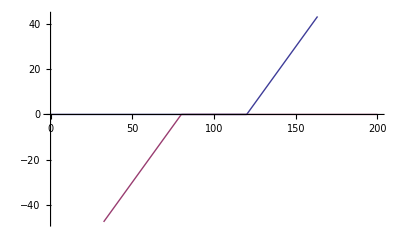

```mathematica
Plot[{OptionPayoff[MkOption[long, call, 120], S], OptionPayoff[MkOption[short, put, 80], S]}, {S, 0, 200}]
```

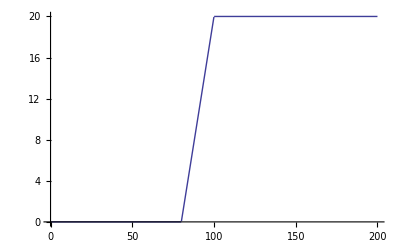

```mathematica
Plot[PortfolioPayoff[{MkOption[long, call, 80],MkOption[short, call, 100]}, S], {S, 0, 200}]
```